# Linearized mBBM Notebook

Solves the eigenvalue problem associated to the linearization of the modified Benjamin-Bona-Mahony equation around a periodic (elliptic function) traveling wave. The notebook computes the spectrum on  using a spectral decomposition and also computes the Hamiltonian Floquet discriminant and bifurcation index using the Mathematica ODE solver. The solutions are computed using the exact elliptic function formulas but are checked at certain points by numerical solution of the traveling wave ODEs. 

The code below solves the traveling wave ODE numerically, for comparison to the analytic solution.

```mathematica
mm =1/2 + Sqrt[5]/10;
c=1;
En =  mm(1-mm)/(2mm-1)^2;
α = Sqrt[2mm/(2mm-1)];
β = Sqrt[1/(2mm-1)];
a = 0;
Abel[ϕ_,E_,a_,c_] := 2 E/c + 2 a ϕ/c + ϕ^2 -ϕ^(4)/(2 c )
RootList=N[x /.Solve[Abel[x,En,a,c]==0,x,Reals,WorkingPrecision->30]];
root2=RootList[[Dimensions[RootList][[1]]]];
root1=RootList[[Dimensions[RootList][[1]]-1]];
avg = (root2+root1)/2;
rad = (root2-root1)/2;
ReducedPoly = PolynomialQuotient[Abel[x,En,a,c],(x-root1)(root2-x),x];
Period = NIntegrate[1/Sqrt[ReducedPoly /. x -> avg + rad Sin[Θ]],{Θ,-Pi,Pi}];
Period2 = 4KI  Sqrt[2mm-1];
WaveProfile = NDSolve[{c y''[x]==a + c y[x] - y[x]^3  ,y[0]==root2,y'[0]==0},y,{x,0,2 Period},AccuracyGoal->13,PrecisionGoal->13];
KI = EllipticK[mm];
KIP = EllipticK[1-mm];
EI = EllipticE[mm];
qq = Exp[- Pi KIP/KI];
An[k_] := 2 Pi α/(Sqrt[mm] KI)  qq^(k+1/2)/(1+qq^(2k+1))
B0 = 6mm/(2mm-1) (EI -(1-mm)KI)/(mm KI) -1
Bn[k_] :=  12Pi^2 mm/(KI^2 mm (2mm-1)) k qq^k/(1-qq^(2k))
nmodes = 15;
PFC = Join[{A0},Table[An[k]/2,{k,1,2*nmodes}]];
WaveProfileF[x_]:= Sum[An[k]Cos[2Pi (2k+1)x/(Period2)],{k,0,nmodes}]
WP[x_] :=Sqrt[2mm/(2mm-1)] JacobiCN[x/Sqrt[2mm-1],mm]
Pot[x_] := 6mm/(2mm-1)( JacobiCN[x/Sqrt[2mm-1],mm])^2-1
Potp[x] := -1/(-1+2 (1/2+1/(2 √5)))^(3/2)12 (1/2+1/(2 √5)) JacobiCN[x/(√(-1+2 (1/2+1/(2 √5)))),1/2+1/(2 √5)] JacobiDN[x/(√(-1+2 (1/2+1/(2 √5)))),1/2+1/(2 √5)] JacobiSN[x/(√(-1+2 (1/2+1/(2 √5)))),1/2+1/(2 √5)];
PotF[x_] := B0 + Sum[Bn[k] Cos[4 Pi k x/Period2],{k,1,nmodes}]
(* WPP[x_] := *)
```

-1+(6 (EllipticE[1/2+1/(2 √5)]-(1/2-1/(2 √5)) EllipticK[1/2+1/(2 √5)]))/((-1+2 (1/2+1/(2 √5))) EllipticK[1/2+1/(2 √5)])

```mathematica
D[Pot[x],x]
```

-1/(-1+2 (1/2+1/(2 √5)))^(3/2)12 (1/2+1/(2 √5)) JacobiCN[x/(√(-1+2 (1/2+1/(2 √5)))),1/2+1/(2 √5)] JacobiDN[x/(√(-1+2 (1/2+1/(2 √5)))),1/2+1/(2 √5)] JacobiSN[x/(√(-1+2 (1/2+1/(2 √5)))),1/2+1/(2 √5)]

The plots below depict the numerical solution of the wave profile and the derivative of the wave profile, and the difference between the wave profile output from the ODE solver and the elliptic function wave profile, as well as the difference between the exact elliptic function wave profile and the the first 2*nmodes+1 terms of the Fourier series for the wave profile. Note that 31 terms of the Fourier series gives a significantly better approximation than the ODE solver.

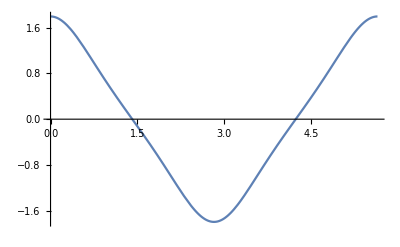

```mathematica
Plot[WP[x],{x,0,Period}]
```

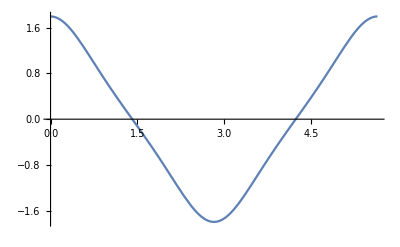

```mathematica
Plot[Evaluate[y[x]]/. WaveProfile,{x,0,Period}]
```

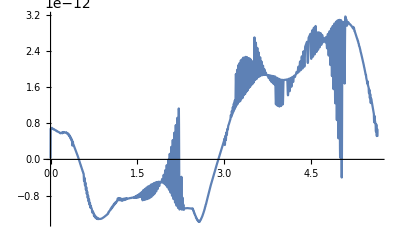

```mathematica
Plot[WP[x]-Evaluate[y[x]]/. WaveProfile,{x,0,Period}]
```

```mathematica
Plot[WaveProfileF[x],{x,0,Period}]
```

-Graphics-

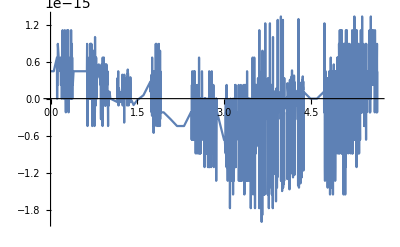

```mathematica
Plot[WaveProfileF[x]-WP[x],{x,0,Period}]
```

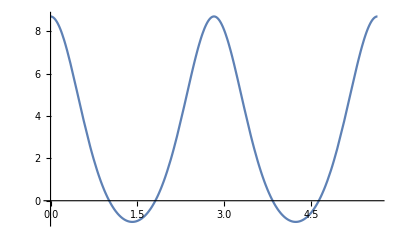

```mathematica
Plot[Pot[x],{x,0,Period}]
```

```mathematica
Plot[Evaluate[3*(y[x])^2-1]/. WaveProfile,{x,0,Period}]
```

-Graphics-

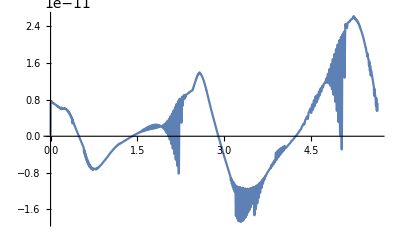

```mathematica
Plot[Pot[x]-Evaluate[3*(y[x])^2-1]/. WaveProfile,{x,0,Period}]
```

```mathematica
Plot[PotF[x],{x,0,Period}]
```

-Graphics-

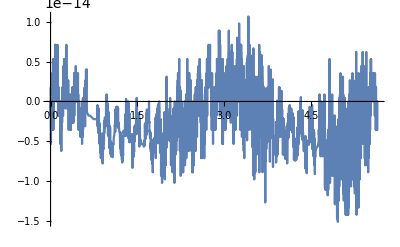

```mathematica
Plot[PotF[x]-Pot[x],{x,0,Period}]
```

Set up the matrices needed for the spectral method. We are solving , where  is the Floquet exponent or quasi-momentum. We will repeatedly solve this eigenvalue problem for different value of μ. As set up μ ranges over the interval .

```mathematica
κ=2 Pi/Period;
J[μ_]:= DiagonalMatrix[Table[I (k+μ)κ/(1+κ^2(k+μ)^2),{k,-nmodes,nmodes}]]
D1[μ_]:= DiagonalMatrix[Table[I (k+μ)κ,{k,-nmodes,nmodes}]]
P[μ_] :=  DiagonalMatrix[Table[(1+κ^2(k+μ)^2),{k,-nmodes,nmodes}]]
L[μ_] := DiagonalMatrix[Table[κ^2(k+μ)^2,{k,-nmodes,nmodes}]]
PFC=Table[0,{i,1,2*nmodes+1}]
Do[PFC[[2*k+2]]=An[k]/2,{k,0,nmodes-1}]
PFC2=Table[0,{i,1,2*nmodes+1}];
PFC2[[1]]=B0;
Do[PFC2[[2*i+1]] = Bn[i]/2,{i,1,nmodes}];
qm = ToeplitzMatrix[PFC2];
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
N[PFC2]
```

{3.09008,0.,2.38148,0.,0.377175,0.,0.0450849,0.,0.00479054,0.,0.00047721,0.,0.0000456358,0.,4.24294×10^-6,0.,3.86432×10^-7,0.,3.4645×10^-8,0.,3.0677×10^-9,0.,2.68918×10^-10,0.,2.33788×10^-11,0.,2.01837×10^-12,0.,1.7322×10^-13,0.,1.47903×10^-14}

At μ=0 the problem should have a zero eigenvalue of algebraic multiplicity three, geometric multiplicity two. This is a good test of the accuracy of the numerics. Here we see that the error in the zero eigenvalues is of order .

```mathematica
N[PFC]
```

{0.,0.822583,0.,0.0707416,0.,0.00564037,0.,0.000449494,0.,0.000035821,0.,2.85465×10^-6,0.,2.27493×10^-7,0.,1.81293×10^-8,0.,1.44476×10^-9,0.,1.15136×10^-10,0.,9.17542×10^-12,0.,7.31208×10^-13,0.,5.82714×10^-14,0.,4.64376×10^-15,0.,3.70071×10^-16,0.}

```mathematica
Dimensions[PFC]
```

{31}

```mathematica
Chop[Eigenvalues[J[0].(L[0]-qm)]]
```

{0.-16.4508 ⅈ,0.+16.4508 ⅈ,0.-15.3227 ⅈ,0.+15.3227 ⅈ,0.-14.1825 ⅈ,0.+14.1825 ⅈ,0.+13.048 ⅈ,0.-13.048 ⅈ,0.-11.9094 ⅈ,0.+11.9094 ⅈ,0.+10.7662 ⅈ,0.-10.7662 ⅈ,0.+9.61691 ⅈ,0.-9.61691 ⅈ,0.+8.45937 ⅈ,0.-8.45937 ⅈ,0.-7.29075 ⅈ,0.+7.29075 ⅈ,0.+6.10673 ⅈ,0.-6.10673 ⅈ,0.-4.90062 ⅈ,0.+4.90062 ⅈ,0.+3.65812 ⅈ,0.-3.65812 ⅈ,0.-2.32935 ⅈ,0.+2.32935 ⅈ,0.-0.520967 ⅈ,0.+0.520967 ⅈ,-2.14074×10^-9-1.58606×10^-6 ⅈ,2.14074×10^-9+1.58606×10^-6 ⅈ,0}

The code below computes the eigenvalues as μ varies over .

```mathematica
evals=Flatten[Table[Chop[Eigenvalues[J[x].(L[x]-qm)]],{x,-1/2,1/2,.00025}]];
```

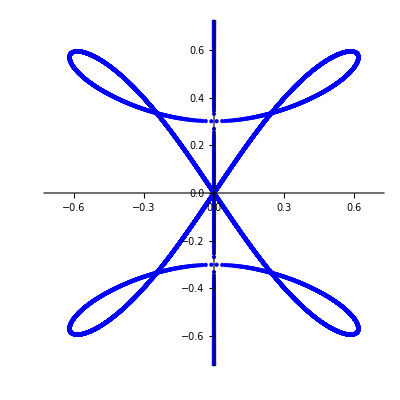

```mathematica
SFig=ComplexListPlot[evals,PlotStyle->{Blue,PointSize[Small]},PlotRange->{{-0.7,0.7},{-0.7,0.7}},AspectRatio->1]
```

```mathematica
Max[Abs[Re[evals]]]
```

0.618387

The code below solves the ODE associated with the linearized operator in order to construct the monodromy map and bifurcation index. The quantities dp[x], dq[x], dr[x] are the derivatives with respect to λ of p[x],q[x],r[x].

```mathematica
sols1=
ParametricNDSolveValue[{p'[x]== q[x],
q'[x]==r[x],
r'[x]==-λ p[x]-Potp[x] p[x] - Pot[x] q[x] + λ r[x],
dp'[x]== dq[x],
dq'[x]== dr[x],dr'[x]==-λ dp[x] - Potp[x] dp[x] - Pot[x] dq[x] + λ dr[x] -p[x] + r[x],p[0]==1,q[0]==0,r[0]==0,dp[0]==0,dq[0]==0,dr[0]==0},{p,q,r,dp,dq,dr},{x,0,25},{λ}];
sols2=
ParametricNDSolveValue[{p'[x]== q[x],
q'[x]==r[x],
r'[x]==-λ p[x]-Potp[x] p[x] - Pot[x] q[x] + λ r[x],
dp'[x]== dq[x],
dq'[x]== dr[x],dr'[x]==-λ dp[x] - Potp[x] dp[x] - Pot[x] dq[x] + λ dr[x] -p[x] + r[x],p[0]==0,q[0]==1,r[0]==0,dp[0]==0,dq[0]==0,dr[0]==0},{p,q,r,dp,dq,dr},{x,0,25},{λ}];
sols3=
ParametricNDSolveValue[{p'[x]== q[x],
q'[x]==r[x],
r'[x]==-λ p[x]-Potp[x] p[x] - Pot[x] q[x] + λ r[x],
dp'[x]== dq[x],
dq'[x]== dr[x],dr'[x]==-λ dp[x] - Potp[x] dp[x] - Pot[x] dq[x] + λ dr[x] -p[x] + r[x],p[0]==0,q[0]==0,r[0]==1,dp[0]==0,dq[0]==0,dr[0]==0},{p,q,r,dp,dq,dr},{x,0,25},{λ}];
```

```mathematica
mon[λ_?NumericQ] := {{sols1[λ][[1]][Period],sols2[λ][[1]][Period],sols3[λ][[1]][Period]},{sols1[λ][[2]][Period],sols2[λ][[2]][Period],sols3[λ][[2]][Period]},{sols1[λ][[3]][Period],sols2[λ][[3]][Period],sols3[λ][[3]][Period]}};
CharPoly[λ_?NumericQ] :=CharacteristicPolynomial[mon[λ],μ];
f[λ_?NumericQ]:=sols1[λ][[1]][Period]+sols2[λ][[2]][Period]+sols3[λ][[3]][Period]
fp[λ_?NumericQ] :=sols1[λ][[4]][Period]+sols2[λ][[5]][Period]+sols3[λ][[6]][Period]
g[λ_?NumericQ] := -1/2(Tr[mon[λ]]^2-Tr[mon[λ].mon[λ]]);
h[λ_?NumericQ] := -Conjugate[g[λ]Exp[-Period λ]];
Δ[λ_?NumericQ] := Det[mon[λ]] Exp[-Period λ];
Φ[λ_?NumericQ] := Discriminant[CharacteristicPolynomial[mon[λ],μ],μ]Exp[-2 Period λ]
Multi[λ_?NumericQ] := If[Re[Discriminant[CharacteristicPolynomial[mon[λ],μ],μ]Exp[-2 Period λ]]<0,1,I]
CP[F_,λ_] := -x^3 + F[λ] x^2 - F[-λ] Exp[Period λ/c] x + Exp[Period λ/c]
```

Again a check of accuracy: the monodromy matrix at λ=0 should have μ=1 as an eigenvalue of multiplicity three. We can see that this is the case, to within about 5 x10^-4.

```mathematica
MatrixForm[mon[0.0]]
Eigenvalues[mon[0.0]]
```

(1. | 3.69844×10^-8 | -1.50958×10^-7
70.943 | 0.999999 | 10.9613
-4.32042×10^-6 | -2.61333×10^-7 | 1.)

{1.00001+0. ⅈ,0.999998+0.000490684 ⅈ,0.999998-0.000490684 ⅈ}

```mathematica
CharPoly[0.0]
```

1.-3. μ+3. μ^2-μ^3

Mark the regions of higher spectral multiplicity with parallel magenta lines. (There do not appear to any intervals of multiplicity 3 in the region being plotted)

```mathematica
S1a = ParametricPlot[{.01*Multi[I x],x},{x,-3,3},PlotStyle->Magenta];
S1b = ParametricPlot[{-.01*Multi[I x],x},{x,-3,3},PlotStyle->Magenta]
```

-Graphics-

```mathematica
Res1 = Expand[Resultant[CP[F,λ],D[CP[F,λ],λ],x]Exp[-3Period λ/c]]
Res1 /. {F[λ] -> H, F[-λ]-> Conjugate[H],F'[λ]->HP,F'[-λ]->Conjugate[HP]}
```

180.242-180.242 F[-λ] F[λ]+31.9084 ⅇ^(5.64875 λ) F[-λ]^2 F'[-λ]+31.9084 F[λ] F'[-λ]-11.2975 ⅇ^(5.64875 λ) F[-λ] F'[-λ]^2+1. ⅇ^(5.64875 λ) F'[-λ]^3+31.9084 F[-λ] F'[λ]+31.9084 ⅇ^(-5.64875 λ) F[λ]^2 F'[λ]-16.9463 F'[-λ] F'[λ]-5.64875 F[-λ] F[λ] F'[-λ] F'[λ]+1. F[λ] F'[-λ]^2 F'[λ]-11.2975 ⅇ^(-5.64875 λ) F[λ] F'[λ]^2+1. F[-λ] F'[-λ] F'[λ]^2+1. ⅇ^(-5.64875 λ) F'[λ]^3

180.242+31.9084 ⅇ^(-5.64875 λ) H^2 HP-11.2975 ⅇ^(-5.64875 λ) H HP^2+1. ⅇ^(-5.64875 λ) HP^3-180.242 H Conjugate[H]+31.9084 HP Conjugate[H]+31.9084 H Conjugate[HP]-16.9463 HP Conjugate[HP]-5.64875 H HP Conjugate[H] Conjugate[HP]+1. HP^2 Conjugate[H] Conjugate[HP]+31.9084 ⅇ^(5.64875 λ) Conjugate[H]^2 Conjugate[HP]+1. H HP Conjugate[HP]^2-11.2975 ⅇ^(5.64875 λ) Conjugate[H] Conjugate[HP]^2+1. ⅇ^(5.64875 λ) Conjugate[HP]^3

```mathematica
Bifurcation[H_,HP_,λ_] := 180.24246928589372+31.908379770108898 ⅇ^(-5.648750283922002 λ) H^2 HP-11.297500567844004 ⅇ^(-5.648750283922002 λ) H HP^2+1. ⅇ^(-5.648750283922002 λ) HP^3-180.24246928589372 H Conjugate[H]+31.908379770108898 HP Conjugate[H]+31.908379770108898 H Conjugate[HP]-16.946250851766006 HP Conjugate[HP]-5.648750283922002 H HP Conjugate[H] Conjugate[HP]+1. HP^2 Conjugate[H] Conjugate[HP]+31.908379770108898 ⅇ^(5.648750283922002 λ) Conjugate[H]^2 Conjugate[HP]+1. H HP Conjugate[HP]^2-11.297500567844004 ⅇ^(5.648750283922002 λ) Conjugate[H] Conjugate[HP]^2+1. ⅇ^(5.648750283922002 λ) Conjugate[HP]^3
Bif2[λ_?NumericQ] := Bifurcation[f[λ],fp[λ],λ]
```

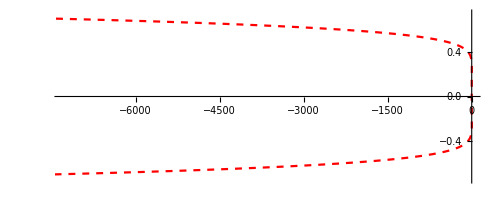

```mathematica
BifPlot=ParametricPlot[{Re[Bif2[I Z]],Z},{Z,-.75,.75},PlotStyle->{Red,Dashed}]
```

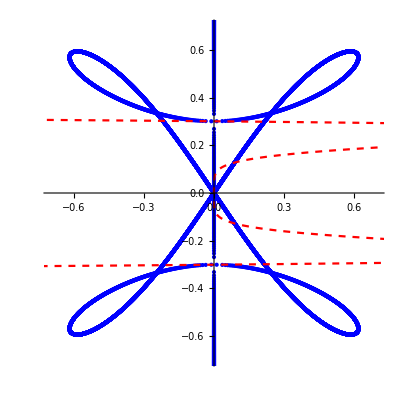

```mathematica
PaperFig=Show[SFig,BifPlot]
```

```mathematica
Export["~/Dropbox/Jared Robby/Schmoopys/BBM/Figure9.png",PaperFig]
```

~/Dropbox/Jared Robby/Schmoopys/BBM/Figure9.png

```mathematica
Export["~/Dropbox/Jared Robby/Schmoopys/BBM/Figure9.pdf",PaperFig]
```

~/Dropbox/Jared Robby/Schmoopys/BBM/Figure9.pdf